Первое задание

```mathematica
X={7.773, 3.117};
```

```mathematica
A={{4.61,0.78},{0.78, 1.22}};
```

```mathematica
B=0.84; n = 30; Hi2=3.665;
```

```mathematica
Ak= Inverse[A]
```

{{0.243231,-0.155509},{-0.155509,0.919096}}

```mathematica
f1=30*{7.773-m1,3.117-m2}.Ak.Transpose[{7.773-m1,3.117-m2}]//Simplify
```

482.703+7.29694 m1^2+m1 (-84.355-9.33052 m2)-99.3632 m2+27.5729 m2^2

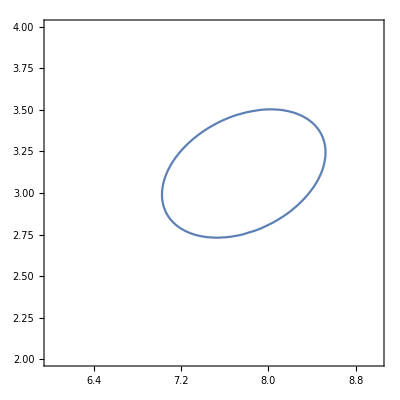

```mathematica
plt1=ContourPlot[f1==Hi2,{m1,6,9},{m2,2,4}]
```

```mathematica
S=1/(n-1)*{{142.4170,15.4004},
{15.4004,29.4517}}
```

{{4.91093,0.531048},{0.531048,1.01558}}

```mathematica
Tb2=4.0557;
```

```mathematica
f2=30*{7.773-m1,3.117-m2}.Inverse[S].Transpose[{7.773-m1,3.117-m2}]//Simplify
```

```mathematica
531.350+6.474 m1^2+m1 (-79.552-6.771 m2)-142.553m2+31.310 m2^2
```

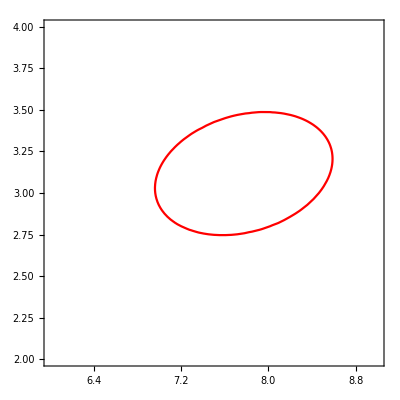

```mathematica
plt2=ContourPlot[f2==Tb2,{m1,6,9},{m2,2,4}, ColorFunction->Hue]
```

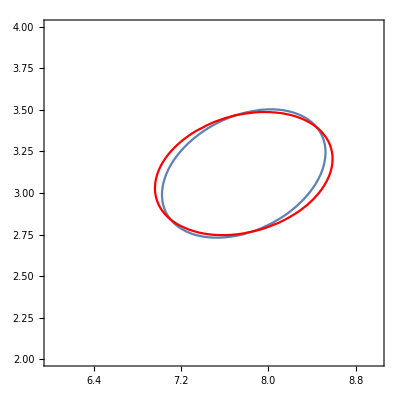

```mathematica
Show[plt1,plt2]
```

Третье задание

```mathematica
n1=30;n2=30;
```

```mathematica
S1=1/(n1-1)*{{632.7328667,-190.4781, 308.4823333},{
-190.4781, 1220.20743, 497.25975},{
308.4823333, 497.25975, 982.0770167}}//MatrixForm
```

(21.8184 | -6.56821 | 10.6373
-6.56821 | 42.0761 | 17.1469
10.6373 | 17.1469 | 33.8647)

```mathematica
({{21.818, -6.568, 10.637}, {-6.568, 42.076, 17.146}, {10.637, 17.146, 33.864}})
```

```mathematica
S2=1/(n2-1)*{{1467.532137, 336.4458033,-115.1908467},{
336.4458033, 6069.4457, 3616.6688},{
-115.1908467, 3616.6688, 2840.2412}}//MatrixForm
```

(50.6046 | 11.6016 | -3.9721
11.6016 | 209.291 | 124.713
-3.9721 | 124.713 | 97.9394)

```mathematica
({{50.604, 11.601, -3.972}, {11.601, 209.291, 124.712}, {-3.972, 124.712, 97.939}})
```

```mathematica
d=S1//FullSimplify
d1=S2
```

29 (21.8184 | -6.56821 | 10.6373
-6.56821 | 42.0761 | 17.1469
10.6373 | 17.1469 | 33.8647)

29 (50.6046 | 11.6016 | -3.9721
11.6016 | 209.291 | 124.713
-3.9721 | 124.713 | 97.9394)

```mathematica
S=({{21.818, -6.568, 10.637}, {-6.568, 42.076, 17.146}, {10.637, 17.146, 33.864}})+({{50.604, 11.601, -3.972}, {11.601, 209.291, 124.712}, {-3.972, 124.712, 97.939}})//MatrixForm
```

(72.422 | 5.033 | 6.665
5.033 | 251.367 | 141.858
6.665 | 141.858 | 131.803)

```mathematica
S*29/58//MatrixForm
```

```mathematica
({{10.909, -3.284, 5.3185}, {-3.284, 21.038, 8.573}, {5.3185, 8.573, 16.932}})
```

```mathematica
k=3;
```

```mathematica
ro=1-((1/(n1-1)-1/(60-2))+(1/(n2-1)-1/(60-2)))*(2 k^2+3k-1)/(6*(k+1))//N
```

0.962644

```mathematica
teta=-ro*(((n1-1)*Log[Det[S1]]-(60-2)*Log[Det[S]])+(n2-1)*Log[Det[S2]]-(60-2)*Log[Det[S]])
```

689.227

```mathematica
tetaCrit =6.251
```

6.251

гипотеза не принимается
Задание 2

```mathematica
n1={4.68,5,1.79,4.53,7.15,3.89,4.31,4.93,3.12,3.39,2,1.29,3.01,4.41,2.92,4.04,4.37,3.65,1.98,3.95,4.2,2.06,2.78,3.27,3.82,3.41,4.36,2.21,4.67,2.36};
n2={-1,69,-7,-5.15,-6.17,-7.1,-2.3,-2.9,-6.84,-1.69,-4.58,-1,-3.32,-1.88,-3.88,-6.02,-5.23,-4,-7.21,-6.17,-3.92,-3.65,-5.72,-3.9,-3.85,-6.25,-2.51,-5.86,-6.22,-6.22,-1.07};
n3={2.87,2.44,4.9,3.12,1.54,1.49,1.8,3.06,3.66,2.91,2.9,3.7,2.91,1.7,3.13,3.23,3.03,4.18,5.42,1.67,2.25,3.02,4.53,2.78,3.45,1.91,4,4.26,3.74,3.92};
```

```mathematica
mu ={0.5, 2.3,4.35};
```

```mathematica
t=RandomVariate[NormalDistribution[],{100,3}];
```

```mathematica
A = {{1.61, -0.14, -1.03},{-0.14, 2.85, -0.64},{-1.03,-0.64,1.22}};
```

```mathematica
CC=CholeskyDecomposition[A]
```

{{1.26886,-0.110335,-0.811754},{0.,1.68458,-0.433083},{0.,0.,0.611142}}

```mathematica
ConjugateTranspose[%].%//MatrixForm
```

(1.61 | -0.14 | -1.03
-0.14 | 2.85 | -0.64
-1.03 | -0.64 | 1.22)

```mathematica
Mu={};
```

```mathematica
tt=t.CC;
```

```mathematica
For[i=1, i <=100,i++,AppendTo[Mu,mu] ]
```

Выборка построена

```mathematica
Cs=tt+Mu//MatrixForm
```

(0.280514 | 2.78695 | 4.08377
1.46736 | 2.67413 | 3.5713
-0.769122 | 2.07575 | 4.92008
0.272542 | 0.790907 | 3.7959
-0.180862 | 0.686657 | 4.90076
0.781838 | -1.06984 | 4.88222
-0.550927 | 2.32991 | 4.86591
-0.557941 | 2.23968 | 4.76019
1.43013 | -0.871416 | 4.90033
3.03338 | 1.65289 | 2.851
-2.37794 | 1.8006 | 6.32963
0.982419 | 4.61154 | 2.81252
-1.72978 | 0.539102 | 7.42354
-1.85473 | 5.74102 | 4.85268
1.67479 | 4.05658 | 3.49812
2.17947 | -1.07299 | 3.42624
-0.149322 | 1.52203 | 4.92164
0.866146 | 1.22986 | 3.71853
1.00191 | -0.584248 | 5.07531
0.0313765 | -1.257 | 5.00914
-0.0505285 | 2.27193 | 2.76172
3.327 | 2.51366 | 1.80934
1.79875 | 1.80624 | 4.29578
-1.17267 | 4.51426 | 4.91988
-0.632742 | 1.64366 | 5.11211
0.545699 | -0.730953 | 5.04135
-1.79613 | 1.80506 | 5.09339
-0.369678 | 3.04398 | 4.51214
0.993678 | 0.311564 | 4.85212
-0.604993 | 3.05099 | 5.13464
-2.63501 | 1.95238 | 6.5995
0.495408 | 0.585168 | 3.84994
-1.97202 | 2.87353 | 5.4951
0.795623 | 3.27511 | 3.2376
-0.101347 | 3.02079 | 4.99168
0.0204815 | 2.51986 | 3.97084
1.31571 | 1.4184 | 3.32112
0.810869 | 1.72334 | 4.37342
0.329438 | 2.34952 | 5.32456
1.06385 | 2.90301 | 3.72392
0.0974093 | 3.72257 | 3.60581
2.84575 | 2.26987 | 1.03699
-0.0198478 | 1.82435 | 4.02168
-0.798345 | 0.60497 | 5.6323
1.26388 | 6.07197 | 3.75398
1.24215 | 1.77768 | 4.33401
-0.518418 | 1.18739 | 4.54854
1.43336 | 2.51033 | 3.60057
-0.349918 | 5.35202 | 4.74529
1.54655 | 2.86322 | 4.0009
-1.09275 | 2.8466 | 4.9659
0.619849 | -0.0656142 | 3.86362
1.13047 | 0.647297 | 4.04031
2.7591 | 1.95263 | 1.95359
-0.338664 | 2.14198 | 4.46588
1.82109 | 1.20888 | 3.72468
1.71647 | 1.53551 | 4.03582
0.326998 | 0.787001 | 4.23905
1.84865 | 5.69687 | 2.76244
0.628998 | 5.06626 | 2.27096
-0.385334 | 2.27199 | 3.99451
1.04041 | 1.26822 | 4.8071
2.88454 | -1.28283 | 3.26496
-0.190896 | 2.23409 | 6.2773
2.39564 | 0.465689 | 3.26418
-0.398192 | -0.961247 | 6.29996
2.98383 | 3.65603 | 1.87961
0.186378 | -0.391268 | 6.29549
-0.279026 | 6.26054 | 3.65407
1.72541 | 1.99005 | 3.63363
1.00978 | 2.80831 | 4.6343
-0.0908508 | 2.94352 | 4.71349
1.09663 | 1.25016 | 4.06825
-1.71202 | 0.760465 | 5.73975
-0.28793 | 0.994379 | 5.85449
0.314447 | -0.665019 | 5.27561
-0.437818 | 2.65604 | 4.75942
1.08489 | 5.13603 | 2.86934
-0.163436 | 2.02743 | 5.20478
3.07293 | 3.37242 | 2.76976
-0.54535 | 5.68073 | 3.32993
0.0956995 | 0.370434 | 4.64858
1.06626 | 4.36226 | 3.48906
-0.178651 | 0.908633 | 5.41456
2.239 | 1.43741 | 3.90259
0.0960988 | -0.693722 | 5.25371
0.501843 | 0.835895 | 4.91738
0.282065 | 3.92376 | 3.54937
2.41306 | 3.64063 | 3.03748
-0.934687 | 0.415376 | 6.8238
0.443257 | -0.534745 | 5.07232
3.11287 | 3.61866 | 1.82807
-1.73195 | 4.48999 | 5.19438
-0.0866918 | 4.5631 | 3.61948
1.00512 | 5.79254 | 3.05854
1.00156 | 0.400328 | 4.48744
1.927 | 4.63266 | 3.81628
2.66018 | 4.27686 | 1.46275
0.648166 | 1.17781 | 3.71007
0.673519 | 3.90133 | 3.37348)

```mathematica
Am=1/100*{{181.625, 9.115, -116.69},{9.115, 271.159,-79.356},{-116.69,-79.356,128.946}}//MatrixForm
Xm = {0.55,2.02,4.46};
A0 = {{1.61, -0.14, -1.03},{-0.14, 2.85, -0.64},{-1.03,-0.64,1.22}}//MatrixForm
mu ={0.5, 2.3,4.35};
```

(1.81625 | 0.09115 | -1.1669
0.09115 | 2.71159 | -0.79356
-1.1669 | -0.79356 | 1.28946)

(1.61 | -0.14 | -1.03
-0.14 | 2.85 | -0.64
-1.03 | -0.64 | 1.22)

```mathematica
lambda = Det[Am.Inverse[A0]]^(1/2*100)Exp[1/2*100*(3-Tr[Am.Inverse[A0]]-Transpose[Xm-mu].Inverse[A0].(Xm-mu))]
```

0.0254058

```mathematica
theta = -2*Log[%]
```

7.34555

Четвертое задание

```mathematica
Am=1/30{{434.3157, 143.11086,1.147683},{143.1086,159.7665, 8.175433},{1.147683, 8.175433, 6.503217}}
```

{{14.4772,4.77036,0.0382561},{4.77029,5.32555,0.272514},{0.0382561,0.272514,0.216774}}

```mathematica
lambda=Det[Am]^(30/2)/(14.9764^15*5.509191^15*0.224249^15);
```

```mathematica
ro=1-(2*3+11)/(6*30)//N
```

0.905556

```mathematica
v=1/2*3(3-1);
```

```mathematica
theta=-2*ro*Log[lambda]
```

14.6335